# -Graphics-

# Wolfram Language Basics

## using notebooks effectively

-Graphics-

## Outline

The Wolfram Language™ provides a familiar user interface to its many features through notebooks.

Introduction to Wolfram Notebooks™

Working with notebooks

Editing, similar in functionality to word processors, providing outlining, formatting, spellchecking and so on

Stylesheets, separating document formatting from content

Interactive elements such as hyperlinks and buttons

Other useful features of notebooks

## Notebooks as Documents

The notebook interface is an editor for documents called notebooks. You can think of notebooks in a similar manner to the files you use in a word processor. There is a menu interface for common tasks such as opening, saving, formatting and printing notebooks. But there are also commands that you will not find in a typical word processor, such as the commands under the Evaluation menu.

Notebooks are stored as plain text files and can be transferred between computers by any method (such as email) that is suitable for transferring text files. As a result, notebooks are portable between different types of computers.

If you would like to see what a notebook file looks like, try opening one with an ordinary text editor.

## The Front End and the Kernel

The Wolfram Language consists of two distinct programs: the kernel and the notebook interface (or notebook front end).

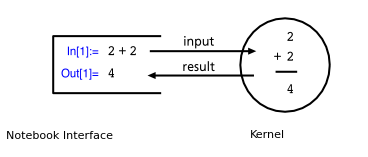

A typical operating cycle consists of the following steps:

Enter input into a notebook window.

Send the input to the kernel for evaluation.

The kernel does the calculation and returns the result.

The front end displays the result in a notebook window.

## Opening More Than One Notebook

The notebook interface normally connects to a single kernel, but just as in a word processor, there may be many open notebooks, each communicating with a single (by default) kernel.

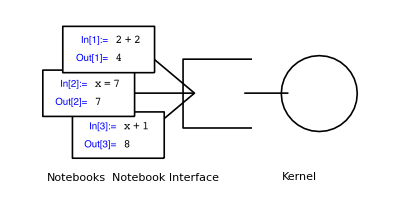

## Working with Cells

Notebooks consist of a list of cells.

Each cell is marked by a cell bracket near the right side of the notebook window.

For example, the cell brackets here indicate an input cell and an output cell:

```mathematica
2+2
```

4

## Creating New Cells

The location of a new cell is marked by a horizontal line called the cell insertion bar. When you start typing, a new cell is created automatically at that point.

You can position the cell insertion bar by clicking between cells.

-Graphics-

Demonstration: Enter a third cell between these two cells:

```mathematica
2+2
```

```mathematica
{1,2,3,4,5}
```

## Cell Styles

There are many different styles of cells.

The style of a cell determines the default characteristics of the cell, such as the font and font size to use when the cell is displayed.

Here is an input cell followed by an output cell. Note the differences in the font used in each cell:

```mathematica
Expand[(a+b)^2]
```

a^2+2 a b+b^2

Messages are shown in message cells:

```mathematica
Cos[1,2]
```

Cos::argx: Cos called with 2 arguments; 1 argument is expected.

Cos[1,2]

## Controlling Cell Style

The style of a cell can be changed by selecting the cell bracket and choosing a style from the Style submenu of the Format menu.

You can also specify the style of a new cell by choosing the cell style from the Style submenu before entering the cell.

## Opening and Closing Cells

Cells can be grouped, and groups can be collapsed.

By default, some cell styles automatically group other styles.

Cell grouping can be performed manually, too.

A cell group can be opened or closed by double-clicking the corresponding cell bracket.

Demonstration: Open and close cell groups in this notebook by double-clicking outer cell brackets.

### This Is a Subsection Cell; It Groups Many Other Cell Types

#### This is a subsubsection cell. It is grouped by the subsection cell.

This is a text cell:

```mathematica
StringSplit["Input cells form their own groups with output cells."]
```

## Example

Open a new notebook.

Create a Section cell and a Text cell.

Create various input, output or graphics cells.

Create another Section cell.

Open and close the cells.

Notebook structure can be used in this way to organize notes, calculations, programs, graphics and other information.

## Entering Special Characters

Special characters can be entered using the following:

Palettes

Palettes are opened from the Palettes menu.

For example, click the π button in the Basic Math Assistant palette.

Keyboard aliases (entered using the Escape key, Esc)

Esc p Esc displays as π.

Character names

\ [Pi] displays as π.

See the Special Characters guide page for a description of special characters and how to input them.

Character names and aliases are displayed in the top-right display area of the Special Characters palette when any button is clicked.

## Entering Typeset Expressions

Typeset structures (two-dimensional expressions) can be entered using the following:

Palettes

Click the √■ button of the Basic Math Assistant palette to get a template for entering a square root.

The Control key, Ctrl

Ctrl+2+x gives √x.

See the examples on the Mathematical Typesetting guide page or the tutorial Two-Dimensional Expression Input.

## Inline Cells

You can include typeset input in text cells.

The result of ∑_(k=1)^∞ 1/k^2 is π^2/6.

Use Ctrl+9 to start an inline cell and Ctrl+0 to end an inline cell. (You can also use the corresponding menu commands in the Typesetting submenu of the Insert menu.)

## Example

Enter this expression using the keyboard and palettes:

```mathematica
√(β/(π^2+x^2))
```

## Hyperlinks

Notebooks make it very easy to link to webpages, other documents as well as objects within a notebook through the use of hyperlinks. For example, clicking this hyperlink to Wolfram Research will cause your web browser to open to http://www.wolfram.com.

There are several ways to create hyperlinks in your notebooks. Perhaps the simplest is to paste a URL into a text cell in the notebook.

Here is a URL in a text cell:

https://www.wolfram.com/wolfram-u/special-event/study-groups/

Sometimes you will find yourself needing to create a hyperlink from a specific piece of text. To do this:

Highlight the word or phrase you wish to turn into a hyperlink.

From the Insert menu, select Hyperlink.

In the Create Hyperlink dialog box that appears, type in (or paste from your browser) the URL; click OK.

-Graphics-

Note that you could also link to other Wolfram Language notebooks by browsing to a specific notebook on your computer from the Create Hyperlink dialog.

You can also create hyperlinks by using the Hyperlink function.

For example, this creates a hyperlink to www.wolfram.com:

```mathematica
Hyperlink["http://www.wolfram.com"]
```

You can add a label that will display instead of the explicit URL by giving Hyperlink two arguments:

```mathematica
Hyperlink["Wolfram Research","http://www.wolfram.com"]
```

## Buttons

Buttons provide an alternate interface to the Wolfram Language. Instead of typing in a function name together with its arguments and using proper syntax and then pressing Shift+Enter to evaluate, you simply click a button and an action happens automatically.

For example, this button displays the current date when clicked:

```mathematica
Button["Today's date",Print[DateString[]]]
```

Note the need for the Print[...] wrapper since Button does not ordinarily return a value (in this way, it has an attribute similar to Do).

For example, the following button, when clicked, expands out a polynomial, but does not print the output to the notebook:

```mathematica
Button["Expand me",tmp=Expand[(x+y)^5]]
```

You can see that the computation has occurred by looking at the value of the symbol tmp that was set inside the button:

```mathematica
tmp
```

Alternatively, you could create a PasteButton that will paste the expression when the button is clicked:

```mathematica
PasteButton["Today's date",DateString[]]
```

```mathematica
PasteButton["Expand me",Expand[(x+y)^5]]
```

Here is a button to create a new notebook in the front end:

```mathematica
Button["New Document",CreateDocument[]]
```

Another kind of button object creates popup windows. These could be useful if you want someone to click a button and have a small window appear with a message.

This creates a button with a help message:

```mathematica
PopupWindow["Help","Make sure to enclose function arguments with square brackets, not parentheses."]
```

## Stylesheets

Working with stylesheets

Editing stylesheets

## What Are Stylesheets?

The Wolfram Language, like many structured document systems, separates the style or formatting information about a notebook from the content. There are several advantages to this approach:

One edit to the stylesheet applies formatting information to all cells of that style.

Notebooks are given a consistent design.

It is easy to maintain styles for all notebooks that share a common stylesheet.

The default styles of cells are set in the stylesheet for the notebook.

The stylesheet used by a notebook can be chosen from the Stylesheet submenu of the Format menu. Try selecting different stylesheets to apply to your notebook.

Style environments provide variations in the appearance of a style. Such variations allow you to use one stylesheet in several different ways without having to make several similar stylesheets. Try selecting different environments (Format ▶ Screen Environment) to see the effect on how your notebook is displayed.

## Editing Stylesheets

You can edit stylesheets to modify the appearance of any notebook that points at that stylesheet. To do this, select Format ▶ Edit Stylesheet.

Once the Style Definitions notebook opens, you can either edit individual cells styles using the pull-down menus, or you can edit the underlying stylesheet directly by clicking its hyperlink at the top of the Style Definitions notebook.

## Slide Shows

You can create slide show–style presentations with the Wolfram Language using new or previously created notebooks. Much of the work in creating a slide show is simplified through the use of the Slide Show palette (found under the Palettes menu).

To create a new slide show notebook, click the New Slide Show button on the Slide Show palette. This will open a new notebook containing three template slides.

Edit the slides, adding text and input cells as you normally would in any Wolfram Language notebook.

To add new slides, either click the Slide Template button on the Slide Show palette or copy and paste an existing slide.

When you are ready to view the notebook as a slide show, select SlideShow under the View Environment pull-down on the Slide Show palette. Or, from the menus, select Format ▶ Screen Environment ▶ SlideShow.

Alternatively, you can convert an existing notebook to a slide show using the Slide Show from Current Document button on the Slide Show palette. Notebooks are easiest to convert to slide shows if you have been consistent in the way you have constructed your notebook. For example, if you think of the Section style as the marker for a new slide, the process will be very easy. In any case, once you have converted a notebook, you should always run through the slide show to make sure you have slides where you want them. You can always use the palette to add additional slides, and by selecting the cell bracket you can delete a navigation bar and merge two slides into one. You can try the convert notebook approach using the sample notebook for slide show presentations that is included with the course materials.

Sample Notebook

Basically you use the Working environment for editing your slide shows and use the SlideShow environment for viewing the slide show. Environments are selected either from the Slide Show palette or from the Format ▶ Screen Environment menu.

You should notice that the Slide Show palette provides additional tools to change the presentation size, adjust magnification and add/delete various window elements.

## Features of Notebooks

### Notebooks Help You Track Computation that was Done Before

In and Out numbers track evaluations in the current session.

Inputs and outputs from earlier sessions have different In/Out flagging.

Mismatched inputs and outputs are called out with dimmed outputs.

Evaluate this to see In/Out lines:

```mathematica
Table[RandomInteger[],10]
```

Quitting the session removes the numbers, but leaves the labels:

```mathematica
Quit
```

Making changes to the input will dim the output:

```mathematica
Plot3D[Cos[x y], {x, 0, 2π},{y,0,2π}]
```

### Notebook Environment Supports Rich Wolfram Language Authoring Experience

Triple-clicking establishes useful structured selections in code.

Use Ctrl+. to expand selections.

Code editor provides completions, templates and other Wolfram Language facilities.

Matching brackets from Insert ▶ Typesetting

Matching []

Matching {}

Matching ()

A random bit of input to demonstrate various selection modes:

```mathematica
Manipulate[
Graphics[GeometricTransformation[First[ArrayPlot[CellularAutomaton[30,{{1},0},20]]],{{a,b},{c,d}}],PlotLabel->NumberForm[MatrixForm[{{a,b},{c,d}}],2]],
{{a,1},-2,2},{{b,0},-2,2},{{c,0},-2,2},{{d,1},-2,2}]
```

### Notebooks Support Rich Data Embedding

Outputs can be turned into inputs; this can help break the dependencies on external data files not available to other readers of your notebook.

Use of nontextual inputs allows for more a comprehensible programming experience.

Data can be “iconized” into concise notebook representations.

Instead of repeatedly fetching this image from the web, embed it into the notebook:

```mathematica
Import["http://www.wolfram.com/homepage/img/feature-system-modeler-5.png"]
```

Or embed a large dataset into the notebook:

```mathematica
Iconize[Import["https://github.com/fivethirtyeight/data/raw/master/nba-elo/nbaallelo.csv"], "FiveThirtyEight NBA data"]
```

### Notebooks Are Fully Computable Entities

Notebook elements are discoverable objects that can be manipulated.

Notebooks can be easily scraped using NotebookImport.

Notebooks and cells are represented as symbolic expressions that can be processed by Wolfram Language programs:

```mathematica
c=EvaluationCell[]
```

```mathematica
CurrentValue[c, Background]=LightBlue;
```

```mathematica
ListPicker[None,NotebookImport[EvaluationNotebook[],"Item"->"Text"]]
```

```mathematica
NotebookRead[c]
```

```mathematica
NotebookWrite[EvaluationNotebook[],% /. "c"->"theCell"]
```

## Exercises

### 10.1 Cell Styles

Create a practice notebook by choosing New from the File menu.

With your practice notebook selected, type “Section One”. By default, this input will become an Input cell.

Select the cell bracket and choose Section from the Format ▶ Style menu to make the cell into a Section cell.

Click in the space below the cell to get a cell insertion bar.

Type “This is some sample text.”

Select the cell bracket and choose Text from the Format ▶ Style menu to make the cell into a Text cell. You can also choose cell styles using the computer keyboard.

Click in the space below the last cell to get a cell insertion bar and type “Section Two”.

Determine the keyboard equivalent of choosing Section from the Format ▶ Style menu. Keyboard equivalents to menu commands are shown in the corresponding menu. In most cases, the keyboard equivalent for Section style will be Alt+4 (or on the Macintosh,  ⌘+4).

Select the cell bracket and use the keyboard to make the cell into a Section cell.

Click the space below the last cell to get a cell insertion bar and enter some sample text.

Select the cell bracket, determine the keyboard equivalent of choosing Text from the Format ▶ Style menu (usually Alt+7 or ⌘+7) and use the keyboard to make the cell into a Text cell. You can also select the cell style before entering the contents of the cell.

Click the space below the last cell to get a cell insertion bar.

Select Section style either by choosing Section from the Format ▶ Style menu or with the keyboard equivalent and type “Section Three”. Your typing should appear in a new Section cell.

Select Text style either by choosing Text from the Format ▶ Style menu or with the keyboard equivalent and enter some sample text. Your typing should appear in a new Text cell.

So far this exercise has only included Section cells and Text cells. If you have time, select a cell and watch the appearance of the cell change as you choose other cell styles listed in the Format ▶ Style menu.

### 10.2 Creating Traditional Mathematical Formulas

Use the palettes in the Palettes menu or keyboard shortcuts to create each of the following formulas:

a_1+a_2+⋯+a_n

s_n=∑_(k=1)^n 1/k

∫_0^∞ 1/(√(1+x^3))ⅆx

(a | b | c
d | e | f
g | h | i)

### 10.3 Editing a Typeset Expression

One way to create typeset input is to edit a similar typeset output.

Evaluate the Integrate input following to get the typeset output ∫f[x]/g[x]ⅆx, then edit the output to replace f[x] with Sqrt[x^2] and g[x] with Sin[x].

```mathematica
Integrate[f[x]/g[x],x]
```

Do you think that the Integrate function will be able to do the resulting integral? Try it and find out. How can you check to see if the result is correct?

### 10.4 Formatting a List of Items

Create a bulleted list from the following four Text cells by selecting the cell brackets and choosing a cell dingbat for the selected cells. Then (with the cells still selected) change the cell margins by choosing Window ▶ Show Ruler and using the ruler toolbar to set the margins.

Symbolic mathematics

Numeric mathematics

Graphics

Typeset editing

### 10.5 Working with Cells

Click the following button to create a sample notebook that you will work on in this exercise. This notebook includes two Section cells and several Text cells. The cells have been grouped using automatic cell grouping, so Text cells are grouped with preceding Section cells. This default cell grouping can be seen from the cell brackets.

Create sample notebook

Follow the instructions in the sample notebook to merge and divide cells and change the grouping of some groups of cells.

### 10.6 Choosing Different Stylesheets

Open a new notebook and enter a Section cell, a Text cell and an Input cell. The contents of these cells can be whatever you want. For example, the contents of the Section cell can be “First Section”, the contents of the Text cell can be “This is a Text cell” (without the double quote marks), and the contents of the Input cell can be 2 + 2.

With your new notebook selected, choose a stylesheet that includes the EquationNumbered style. You can choose a stylesheet from the Stylesheet submenu of the Format menu. Observe how your notebook changes as you change the stylesheet. When you find a stylesheet that includes the EquationNumbered style, enter an EquationNumbered cell in your notebook.

Hint

You can find a stylesheet that includes the EquationNumbered style by choosing stylesheets one at a time and for each stylesheet looking for EquationNumbered among the available styles. The available styles for each stylesheet will be listed in the Style submenu of the Format menu.

Solution

### 10.7 Typesetting within Text

You can include typesetting within a Text cell by creating an inline cell. You can start entering an inline cell by pressing Ctrl+( or Ctrl+9 (pressing the 9 key while holding down the Ctrl key). Within the inline cell you can use the same palettes and keystrokes that you would use for entering other typeset input or you can paste typesetting from elsewhere in a notebook. When you are finished, you can end the inline cell and return to ordinary text input by pressing Ctrl+) or Ctrl+0.

Open a new notebook and type the following Text cell into the new notebook.

The positive solution of the equation x^2==2 is √2.

Hint

After opening the new notebook, choose Text from the Style submenu of the Format menu or otherwise prepare to enter a Text cell.

Type “The positive solution of the equation ” (without the double quote marks) into the Text cell in the new notebook.

Press the 9 key while holding down the Ctrl key to begin an inline cell.

Type x.

Type Ctrl+6 to get an exponent, and type 2.

Type Ctrl+space to get out of the exponent.

Type “==2” (without the double quote marks).

Type Ctrl+0 to end the inline cell.

Type “is” (without the double quote marks).

Type Ctrl+9 to start a new inline cell.

Type Ctrl+2 to get a square root.

Type 2.

Type Ctrl+0 to end the inline cell.

Type a period to end the sentence.

### 10.8 Notebook Options

Open a new notebook. With the new notebook selected, choose Option Inspector from the Format menu to open the Option Inspector window.

At the top of the Option Inspector window, set the field for “Show option values for” to “Selected Notebook”.

In the Option Inspector, type WindowTitle in the Lookup text field and press Enter.

Type “Notebook Exercise” (including the quotes) or any other window title of your choice into the box at the right of WindowTitle and press Enter. The title at the top of your notebook window should change to the value set by the WindowTitle option.

You might also try setting other options for your notebook window, such as the WindowSize option to change the size of the window or the Background option to change the background color of the notebook.

### 10.9 Adding Entries to a Matrix

Add one row and one column to each matrix in this matrix dot product. Use 1 for the diagonal elements in both matrices, x for the off-diagonal elements in the first matrix and β for the off-diagonal elements in the second matrix:

```mathematica
({{1, x}, {x, 1}}).({{1, β}, {β, 1}})
```

Evaluate the matrix dot product and display the result in MatrixForm. The result should be the following:

(1+2 x β | x+β+x β | x+β+x β
x+β+x β | 1+2 x β | x+β+x β
x+β+x β | x+β+x β | 1+2 x β)